```mathematica
Clear["Global`*"];
(* All in mkm *)
```

```mathematica
λ=1.55;
n=1;
β=(2π n)/λ;
CalcWindow=2000;
N0=511;
ω0=100;
q0=N[(π ω0^2)/(I λ)];
zR=Re[I q0]
```

20268.3

```mathematica
ω[z_]:=N[ω0 √(1+((λ z)/(π ω0^2))^2)];
R[z_]:=N[z(1+((π ω0^2)/(λ z))^2)];
q[z_]:=Piecewise[{{(-1/R[z]+I λ/(π ω[z]^2))^-1,z<0||z>0}},q0];
Gauss[r_,z_]:=N[Exp[I(β r^2)/2 1/q[z]]];
```

```mathematica
LenceSpherical[r_,f_]:=N[Exp[(I β r^2)/(2f)]];
LenceMatrix[f_]:=Array[LenceSpherical[√(#1^2+#2^2),f]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
```

```mathematica
L0=0.;
StartBeam=Array[Gauss[√(#1^2+#2^2),L0]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
ArrayPlot[Arg[StartBeam]];
```

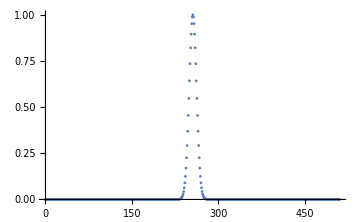
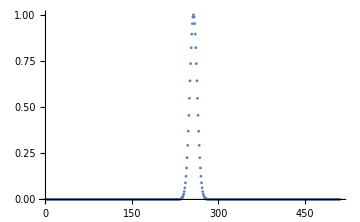

```mathematica
{ListPlot[Abs[StartBeam[[(N0+1)/2]]]^2,PlotRange->All,ImageSize->Medium],
ListPlot[RotateLeft[Abs[Fourier[StartBeam[[(N0+1)/2]]]]^2,(N0-1)/2],PlotRange->All,ImageSize->Medium]}
```

```mathematica
D2Fourier=N[(π/CalcWindow)^2 RotateLeft[Array[(#1^2+#2^2)&,{N0,N0},{-(N0-1)/2,-(N0-1)/2}],{(N0-1)/2,(N0-1)/2}]];
FourierOp[h_]:=Exp[I (D2Fourier h)/(2β)];
```

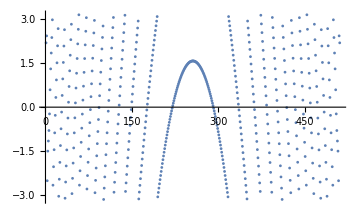
{-Graphics-,-Graphics-}

```mathematica
f=100000.;
LenceBeam=StartBeam LenceMatrix[f];
FinalBeam=InverseFourier[FourierOp[f] Fourier[LenceBeam ]];
{ListPlot[Arg[FinalBeam[[(N0+1)/2]]],ImageSize->Medium,Joined->False],ArrayPlot[Arg[FinalBeam],DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium]}
```

```mathematica
{ArrayPlot[Abs[StartBeam]^2,ColorFunction->"GrayTones",ImageSize->Medium],ArrayPlot[Abs[FinalBeam]^2,ColorFunction->"GrayTones",ImageSize->Medium]}
```

{-Graphics-,-Graphics-}

```mathematica
L=f;
```

```mathematica
Beam=Parallelize[Table[Abs[InverseFourier[FourierOp[l] Fourier[LenceBeam ]][[(N0+1)/2]]]^2,{l,0,L,(L-0)/1000}]];
```

```mathematica
ListPlot3D[Beam,PlotRange->All,ImageSize->Medium,DataRange->{{-CalcWindow,CalcWindow},{0,L}}]
```

-Graphics3D-